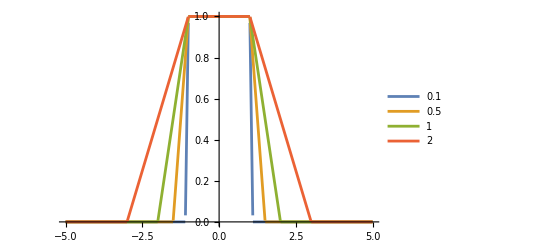

```mathematica
ϕ[x_,δ_]:=Piecewise[{{0,Abs[x]-1>=δ},{(x+1)/δ+1,-1-δ<x<-1},{-(x-1)/δ+1,1<x<1+δ},{1,Abs[x]<=1}}]
δList={0.1,0.5,1,2};
Plot[Evaluate@Table[ϕ[x,δ],{δ,δList}],{x,-5,5},PlotRange->All,PlotLegends->δList]
```

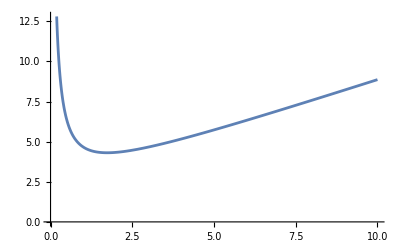

{4.3094,{δ→1.73205}}

```mathematica
Capacity[δ_]:=Integrate[ϕ[x,δ]^2+D[ϕ[x,δ],x]^2,{x,-∞,+∞}]
Plot[Capacity[δ],{δ,0.001,10},AxesOrigin->{0,0}]
FindMinimum[{Capacity[δ],0.001<=δ<=10},{δ,1}]
```

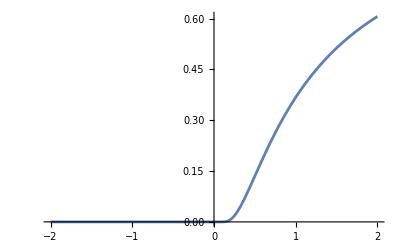

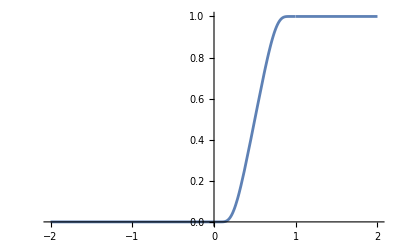

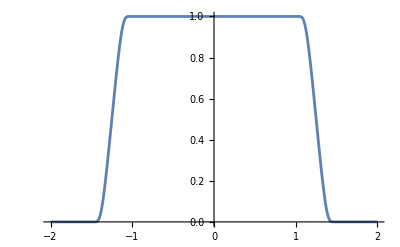

```mathematica
SmoothTrasitionFunction[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x<0}}]
BumpFunction[x_]:=SmoothTrasitionFunction[x]/(SmoothTrasitionFunction[x]+SmoothTrasitionFunction[1-x])
VarBumpFunction[x_,a_,b_,c_,d_]:=If[a<b<c<d,BumpFunction[(x-a)/(b-a)]*BumpFunction[(d-x)/(d-c)],"Undefined"]
Plot[SmoothTrasitionFunction[x],{x,-2,2},AxesOrigin->{0,0}]
Plot[BumpFunction[x],{x,-2,2},AxesOrigin->{0,0}]
Plot[Evaluate@@VarBumpFunction[x,-1.5,-1,1,1.5],{x,-2,2}]
```

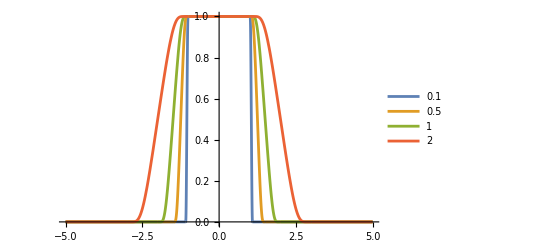

```mathematica
ψ[x_,δ_]:=VarBumpFunction[x,-1-δ,-1,1,1+δ]
Plot[Evaluate@Table[ψ[x,δ],{δ,δList}],{x,-5,5},PlotRange->All,PlotLegends->δList]
```

NIntegrate::ncvb: 在接近 {x} = {-1.00009} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.62301×10^9 和 1.24143×10^9.

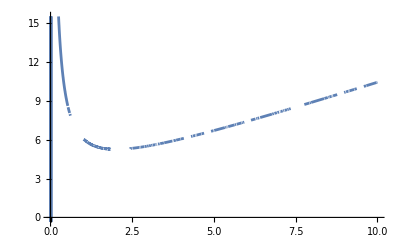

```mathematica
SmoothCapacity[δ_]:=NIntegrate[ψ[x,δ]^2+D[ψ[x,δ],x]^2,{x,-∞,+∞}]
Plot[SmoothCapacity[δ],{δ,0.001,10},AxesOrigin->{0,0}]
```

```mathematica
SmoothCapacity[1.73]
```

NIntegrate::ncvb: 在接近 {x} = {-1.0083826148317} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.29044 和 0.000101786.

5.29044